```mathematica
(*/////////////////ввод параметров///////////////////*)
deltaP=10^6;
mu=0.001;
k=10^(-12);
R=100;
rw=0.001*R;
h1=1;
h2=5;
h3=20;
h4=50;
(*/////////////////относительное вскрытие пласта///////////////////*)
huh[b_,h_]=b/h;
```

```mathematica
(*/////////////////Пункт №1///////////////////*)
(*/////////////////дебит совершенной скважины///////////////////*)
Q[h_,rw_]:=2*π*k*h/mu*deltaP/Log[R/rw];
```

```mathematica
(*/////////////////несовершенные скважины ///////////////////*)
```

```mathematica
(*Н. К. Гиринского*)
Q1[b_,h_,rw_]:=2*π*k*b/mu*deltaP/Log[1.66*b/rw];
```

```mathematica
(*М.Маскета*)
ϕ[x_]=Log[Gamma[0.875*x]*Gamma[0.125*x]/(Gamma[1-0.875*x]*Gamma[1-0.125*x])];

ξ[b_,h_,rw_]:=1/2/huh[b,h]*(2*Log[4*h/rw]-ϕ[huh[b,h]])-Log[4*h/R];
Q2[b_,h_,rw_]:=2*π*k*h/mu*deltaP/ξ[b,h,rw];
```

```mathematica
(*Козени*)
Q3[b_,h_,rw_]:=2*π*k*h*huh[b,h]/mu*deltaP/Log[R/rw]*(1+7*Sqrt[rw/2/h/huh[b,h]]*Cos[π*huh[b,h]/2]);
```

```mathematica
(*И. А. Чарного*)
A=1.5;(*из лекции, обычно берут 1.5*)
R0[h_]=A*h;
Q4[b_,h_,rw_]:=2*π*k*h/mu*deltaP/(Log[R/R0[h]]+h/rw-h/R0[h]);
```

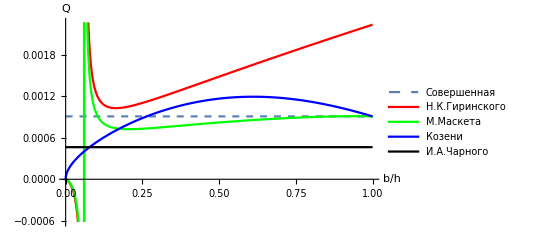

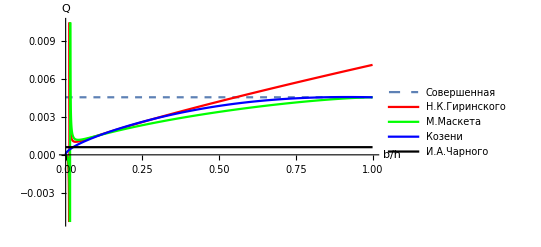

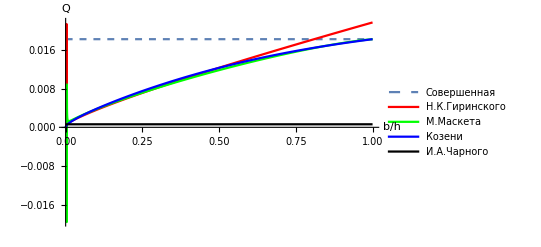

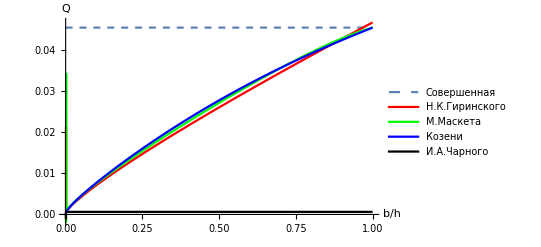

```mathematica
Plot[{Q[h1,rw],Q1[b*h1,h1,rw],Q2[b*h1,h1,rw],Q3[b*h1,h1,rw],Q4[b*h1,h1,rw]},{b,0,1},PlotStyle->{Dashed,Red,Green, Blue,Black},PlotLegends->LineLegend[Automatic,{"Совершенная","Н.К.Гиринского","М.Маскета","Козени","И.А.Чарного"}],AxesLabel->{b/h,Q}]
Plot[{Q[h2,rw],Q1[b*h2,h2,rw],Q2[b*h2,h2,rw],Q3[b*h2,h2,rw],Q4[b*h2,h2,rw]},{b,0,1},PlotStyle->{Dashed,Red,Green, Blue,Black},PlotLegends->LineLegend[Automatic,{"Совершенная","Н.К.Гиринского","М.Маскета","Козени","И.А.Чарного"}],AxesLabel->{b/h,Q}]
Plot[{Q[h3,rw],Q1[b*h3,h3,rw],Q2[b*h3,h3,rw],Q3[b*h3,h3,rw],Q4[b*h3,h3,rw]},{b,0,1},PlotStyle->{Dashed,Red,Green, Blue,Black},PlotLegends->LineLegend[Automatic,{"Совершенная","Н.К.Гиринского","М.Маскета","Козени","И.А.Чарного"}],AxesLabel->{b/h,Q}]
Plot[{Q[h4,rw],Q1[b*h4,h4,rw],Q2[b*h4,h4,rw],Q3[b*h4,h4,rw],Q4[b*h4,h4,rw]},{b,0,1},PlotStyle->{Dashed,Red,Green, Blue,Black},PlotLegends->LineLegend[Automatic,{"Совершенная","Н.К.Гиринского","М.Маскета","Козени","И.А.Чарного"}],AxesLabel->{b/h,Q}]
```

```mathematica
(*/////////////////Пункт №2///////////////////*)
(*/////////////////Дебит горизонтальной скважины///////////////////*)
```

```mathematica
(*Ю.П.Борисова*)
Q5[l_,h_]=2*π*k*h/mu*deltaP/(Log[2*R/l]+h/2/l*Log[h/2/π/rw]);
```

```mathematica
(*-С.Д.Джоши*)
a[l_,h_]=l*Sqrt[0.5+Sqrt[0.25+(R/l)^4]];
Q6[l_,h_]=2*π*k*h/mu*deltaP/(Log[(a[l,h]+Sqrt[(a[l,h])^2-l^2])/l]+h/2/l*Log[h/2/rw]);
```

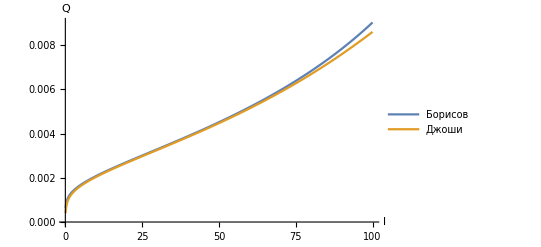

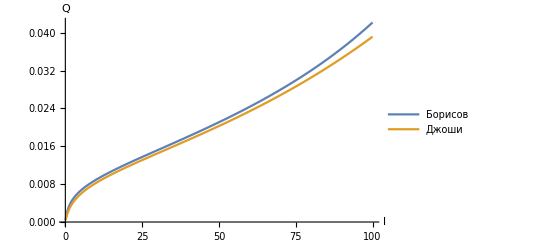

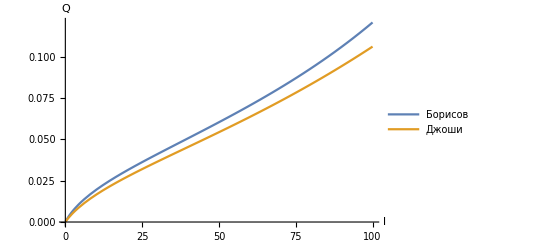

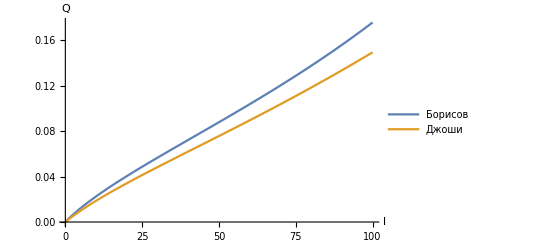

```mathematica
Plot[{Q5[l,h1],Q6[l,h1]},{l,rw,R},PlotLegends->LineLegend[Automatic,{"Борисов","Джоши"}],AxesLabel->{l,Q}]
Plot[{Q5[l,h2],Q6[l,h2]},{l,rw,R},PlotLegends->LineLegend[Automatic,{"Борисов","Джоши"}],AxesLabel->{l,Q}]
Plot[{Q5[l,h3],Q6[l,h3]},{l,rw,R},PlotLegends->LineLegend[Automatic,{"Борисов","Джоши"}],AxesLabel->{l,Q}]
Plot[{Q5[l,h4],Q6[l,h4]},{l,rw,R},PlotLegends->LineLegend[Automatic,{"Борисов","Джоши"}],AxesLabel->{l,Q}]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

General::munfl: 1/16.6^48951. is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-327219.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-4306.39] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

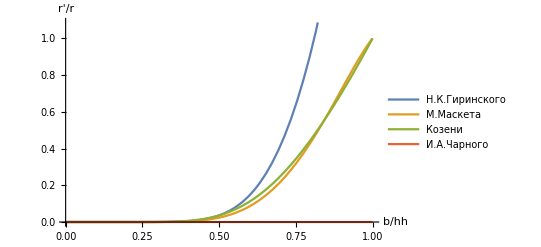

General::munfl: Exp[-327219.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-4306.39] is too small to represent as a normalized machine number; precision may be lost.

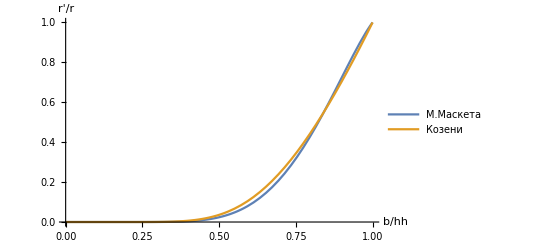

1.

1.

8.08639×10^-85

```mathematica
(*/////////////////Построение графика отношения rc'/rc///////////////////*)

h=h3;
s1=Solve[Q[h,rc]==Q1[b,h,rw],rc][[1,1,2]];
s2=Solve[Q[h,rc]==Q2[b,h,rw],rc][[1,1,2]];
s3=Solve[Q[h,rc]==Q3[b,h,rw],rc][[1,1,2]];
s4=Solve[Q[h,rc]==Q4[b,h,rw],rc][[1,1,2]];
sl1[b_]=s1/rw;
sl2[b_]=s2/rw;
sl3[b_]=s3/rw;
sl4[b_]=s4/rw;
Plot[{sl1[b*h],sl2[b*h],sl3[b*h],sl4[b*h]},{b,0,1},PlotLegends->LineLegend[Automatic,{"Н.К.Гиринского","М.Маскета","Козени","И.А.Чарного"}],AxesLabel->{b/hh,r'/r}]
Plot[{sl2[b*h],sl3[b*h]},{b,0,1},PlotLegends->LineLegend[Automatic,{"М.Маскета","Козени","И.А.Чарного"}],AxesLabel->{b/hh,r'/r}]
sl2[h]
sl3[h]
sl4[h]
```